# Vaja 1

Naloga 1

```mathematica
(1/3+1/6)^2
3/(6/8)
Sin[Π/2]
E^Log[7]
```

1/4

4

Sin[Π/2]

7

Naloga 2

```mathematica
Simplify[((3+4 x)/(2+5 x))^2+((2+x)/(1-x))^2]
```

```mathematica
(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2
Simplify[(x/y)+(y/x)+2]
Simplify[(x^2+y^2)^2-2(xy)^2]
Simplify[Sin[x]^2+Cos[x]^2]
Simplify[2 Sin[x] Cos[x]]
FullSimplify[Tan[π/8]^4+Cot[π/8]^4]
FullSimplify[(278+42 √5-12 √6-28 √30)^(1/2)]
```

(2+x)^2/(-1+x)^2+(3+4 x)^2/(2+5 x)^2

(x+y)^2/(x y)

-2 xy^2+(x^2+y^2)^2

1

Sin[2 x]

34

3+7 √5-2 √6

Naloga 3

```mathematica
TrigExpand[(x+x y+ y)^10]
```

Naloga 4

```mathematica
a=3
b=4
c=6
o:=a+b+c
s:=o/2
√(s(s-1)(s-b)(s-c))  (*Geom pomen=ploščina trikotnika *)
ClearAll[a,b,c,o,s]
```

3

4

6

(√715)/4

Naloga 5

```mathematica
s:={3,20,0,5,13,2,-x,8}
s[[5]]
(*s[[-1]] vrne zadnji element*)
```

13

Naloga 6

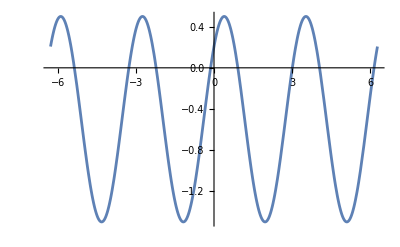

```mathematica
Plot[Sin[2x+π/4]-1/2,{x,-2π,2π}]
```

Naloga 7

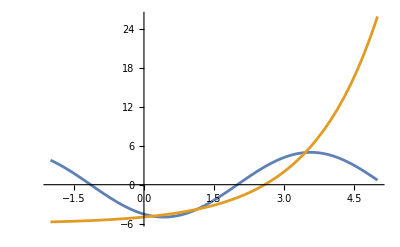

{}

```mathematica
f[x_]:=5 Sin[x-2]
g[x_]:=2^x-6
Plot[{f[x],g[x]},{x,-2,5}]
f[x]==g[x]//Solve (*??*)
```

Naloga 8

```mathematica
a:=3^200+20
b:=2^300+30
a==b
a<b
a>b
```

False

False

True

Naloga 9

```mathematica
Solve[x^2+4 x+2==0]
Solve[x^2+4 x+5==0]
```

{{x→-2-√2},{x→-2+√2}}

{{x→-2-ⅈ},{x→-2+ⅈ}}

Naloga 10

```mathematica
Reduce[x^4==1]
```

x==-1||x==-ⅈ||x==ⅈ||x==1

Naloga 11

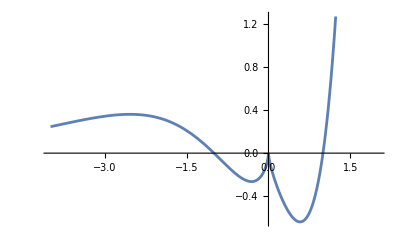

Solve::naqs: ⅇ^x (x^2-(x^2)^(1/3)) is not a quantified system of equations and inequalities.

Solve[ⅇ^x (x^2-(x^2)^(1/3))]

Reduce::naqs: ⅇ^x (x^2-(x^2)^(1/3)) is not a quantified system of equations and inequalities.

Reduce[ⅇ^x (x^2-(x^2)^(1/3))]

3

4

6

(√715)/4

a

```mathematica
f[x_]:=(x^2- CubeRoot[x^2]) E^x
Plot[f[x],{x,-4,2}] (*ničli: x0=-1, x1=0*)
Solve[f[x]]
Reduce[f[x]](*Solve in reduce ne delata*)
```